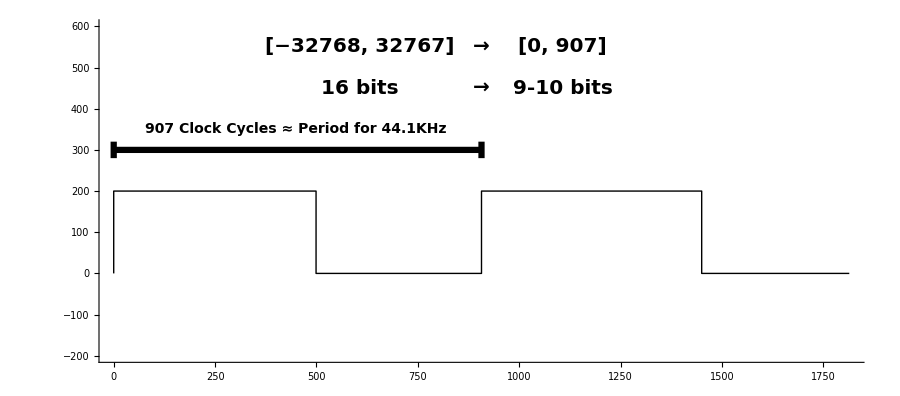

```mathematica
h=300;Graphics[{{Thickness[.005],Line[{{{0,h},{907,h}},{{0,h-20},{0,h+20}},{{907,h-20},{907,h+20}}}]},
{Line[{{{0,0},{0,200},{499,200},{499,0},{907,0},{907,200},{1450,200},{1450,0},{2*907,0}}}]},
{Text[Style["907 Clock Cycles ≈ Period for 44.1KHz",Bold,14],{450,h+50}]},
{Text[Style["[−32768, 32767]",Bold,20],{907-300,550}],Text[Style["→",Bold,20],{907,550}],Text[Style["[0, 907]",Bold,20],{907+200,550}]},
{Text[Style["16 bits",Bold,20],{907-300,450}],Text[Style["→",Bold,20],{907,450}],Text[Style["9-10 bits",Bold,20],{907+200,450}]}

},Axes->{True,False},PlotRange->{{0,907*2},{-200,600}},TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

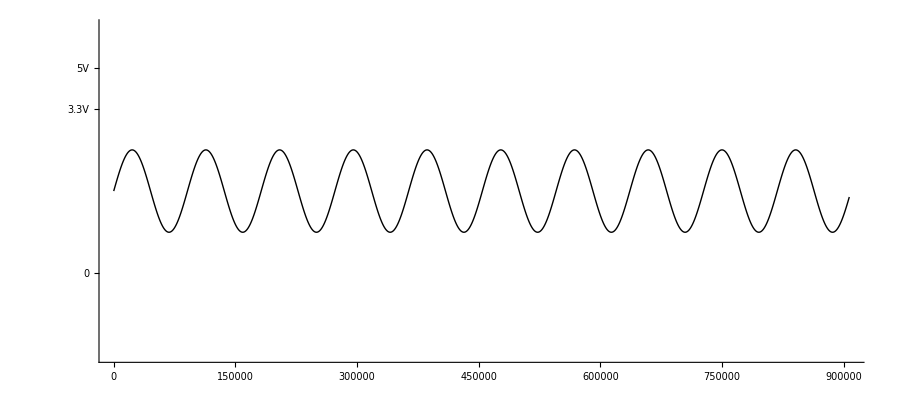

```mathematica
s=500;Graphics[{
Line[Table[{x,100*s*N[Sin[2*Pi*x*440/40000000]+2]},{x,0,907*2*s,s/2}]]},Axes->{True,True},Ticks->{Automatic,{{0,0},{100*s*4,"3.3V"},{100*s*5,"5V"}}},PlotRange->{{0,907*2},{-200,600}}*s,TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

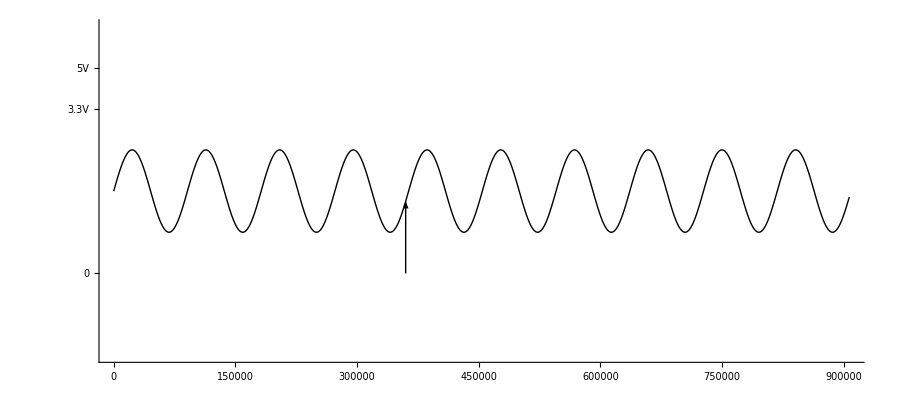

```mathematica
s=500;Graphics[{
Line[Table[{x,100*s*N[Sin[2*Pi*x*440/40000000]+2]},{x,0,907*2*s,s/2}]],
{Arrowheads[Medium],Arrow[{{360000,0},{360000,100*s*N[Sin[2*Pi*360000*440/40000000]+2]}}]}
},Axes->{True,True},Ticks->{Automatic,{{0,0},{100*s*4,"3.3V"},{100*s*5,"5V"}}},PlotRange->{{0,907*2},{-200,600}}*s,TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

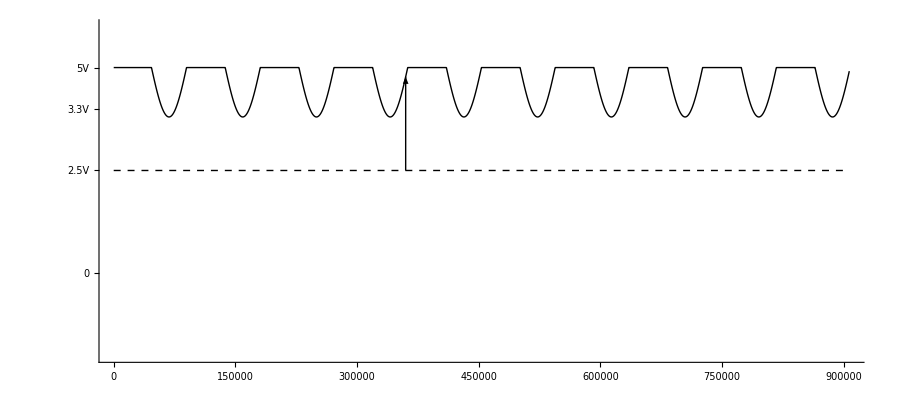

```mathematica
s=500;Graphics[{
Line[Table[{x,Min[1.3*100*s*N[Sin[2*Pi*x*440/40000000]+2]+2.5*s*100,100*s*5]},{x,0,907*2*s,s/2}]],
{Dashed,Line[{{0,2.5*s*100},{907*2*s,2.5*s*100}}]},
{Arrowheads[Medium],Arrow[{{360000,2.5*s*100},{360000,Min[1.3*100*s*N[Sin[2*Pi*360000*440/40000000]+2]+2.5*s*100]}}]}
},Axes->{True,True},Ticks->{Automatic,{{0,0},{100*s*4,"3.3V"},{100*s*2.5,"2.5V"},{100*s*5,"5V"}}},PlotRange->{{0,907*2},{-200,600}}*s,TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

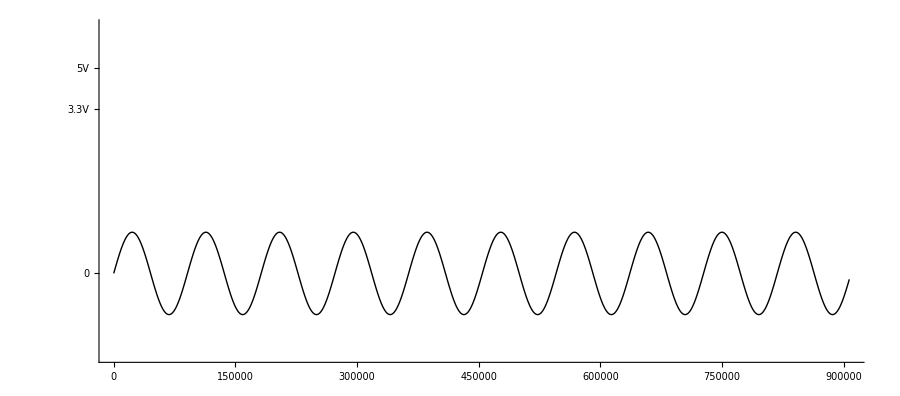

```mathematica
s=500;Graphics[{
Line[Table[{x,100*s*N[Sin[2*Pi*x*440/40000000]]},{x,0,907*2*s,s/2}]]
},Axes->{True,True},Ticks->{Automatic,{{0,0},{100*s*4,"3.3V"},{100*s*5,"5V"}}},PlotRange->{{0,907*2},{-200,600}}*s,TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

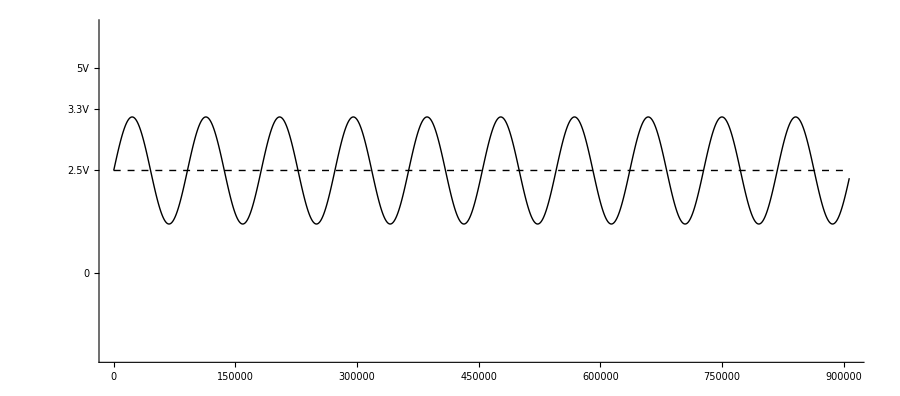

```mathematica
s=500;Graphics[{
Line[Table[{x,Min[1.3*100*s*N[Sin[2*Pi*x*440/40000000]]+2.5*s*100,100*s*5]},{x,0,907*2*s,s/2}]],
{Dashed,Line[{{0,2.5*s*100},{907*2*s,2.5*s*100}}]}
},Axes->{True,True},Ticks->{Automatic,{{0,0},{100*s*4,"3.3V"},{100*s*2.5,"2.5V"},{100*s*5,"5V"}}},PlotRange->{{0,907*2},{-200,600}}*s,TicksStyle->Directive["Label", 14],LabelStyle->{Bold,14},AxesStyle->{Black,Bold},ImageSize->900,AxesLabel->{"40MHz Clock Cycles"}]
```

```mathematica
Table[N[Sin[2*Pi*x*440/40000000]],{x,0,600*5000,10000}]
```

{0.,0.637424,0.982287,0.876307,0.368125,-0.309017,-0.844328,-0.992115,-0.684547,-0.0627905,0.587785,0.968583,0.904827,0.425779,-0.24869,-0.809017,-0.998027,-0.728969,-0.125333,0.535827,0.951057,0.929776,0.481754,-0.187381,-0.770513,-1.,-0.770513,-0.187381,0.481754,0.929776,0.951057,0.535827,-0.125333,-0.728969,-0.998027,-0.809017,-0.24869,0.425779,0.904827,0.968583,0.587785,-0.0627905,-0.684547,-0.992115,-0.844328,-0.309017,0.368125,0.876307,0.982287,0.637424,4.89983×10^-15,-0.637424,-0.982287,-0.876307,-0.368125,0.309017,0.844328,0.992115,0.684547,0.0627905,-0.587785,-0.968583,-0.904827,-0.425779,0.24869,0.809017,0.998027,0.728969,0.125333,-0.535827,-0.951057,-0.929776,-0.481754,0.187381,0.770513,1.,0.770513,0.187381,-0.481754,-0.929776,-0.951057,-0.535827,0.125333,0.728969,0.998027,0.809017,0.24869,-0.425779,-0.904827,-0.968583,-0.587785,0.0627905,0.684547,0.992115,0.844328,0.309017,-0.368125,-0.876307,-0.982287,-0.637424,-9.79965×10^-15,0.637424,0.982287,0.876307,0.368125,-0.309017,-0.844328,-0.992115,-0.684547,-0.0627905,0.587785,0.968583,0.904827,0.425779,-0.24869,-0.809017,-0.998027,-0.728969,-0.125333,0.535827,0.951057,0.929776,0.481754,-0.187381,-0.770513,-1.,-0.770513,-0.187381,0.481754,0.929776,0.951057,0.535827,-0.125333,-0.728969,-0.998027,-0.809017,-0.24869,0.425779,0.904827,0.968583,0.587785,-0.0627905,-0.684547,-0.992115,-0.844328,-0.309017,0.368125,0.876307,0.982287,0.637424,4.88621×10^-16,-0.637424,-0.982287,-0.876307,-0.368125,0.309017,0.844328,0.992115,0.684547,0.0627905,-0.587785,-0.968583,-0.904827,-0.425779,0.24869,0.809017,0.998027,0.728969,0.125333,-0.535827,-0.951057,-0.929776,-0.481754,0.187381,0.770513,1.,0.770513,0.187381,-0.481754,-0.929776,-0.951057,-0.535827,0.125333,0.728969,0.998027,0.809017,0.24869,-0.425779,-0.904827,-0.968583,-0.587785,0.0627905,0.684547,0.992115,0.844328,0.309017,-0.368125,-0.876307,-0.982287,-0.637424,-1.95993×10^-14,0.637424,0.982287,0.876307,0.368125,-0.309017,-0.844328,-0.992115,-0.684547,-0.0627905,0.587785,0.968583,0.904827,0.425779,-0.24869,-0.809017,-0.998027,-0.728969,-0.125333,0.535827,0.951057,0.929776,0.481754,-0.187381,-0.770513,-1.,-0.770513,-0.187381,0.481754,0.929776,0.951057,0.535827,-0.125333,-0.728969,-0.998027,-0.809017,-0.24869,0.425779,0.904827,0.968583,0.587785,-0.0627905,-0.684547,-0.992115,-0.844328,-0.309017,0.368125,0.876307,0.982287,0.637424,-3.92258×10^-15,-0.637424,-0.982287,-0.876307,-0.368125,0.309017,0.844328,0.992115,0.684547,0.0627905,-0.587785,-0.968583,-0.904827,-0.425779,0.24869,0.809017,0.998027,0.728969,0.125333,-0.535827,-0.951057,-0.929776,-0.481754,0.187381,0.770513,1.,0.770513,0.187381,-0.481754,-0.929776,-0.951057,-0.535827,0.125333,0.728969,0.998027,0.809017,0.24869,-0.425779,-0.904827,-0.968583,-0.587785,0.0627905,0.684547,0.992115,0.844328,0.309017,-0.368125,-0.876307,-0.982287,-0.637424,-9.77242×10^-16}

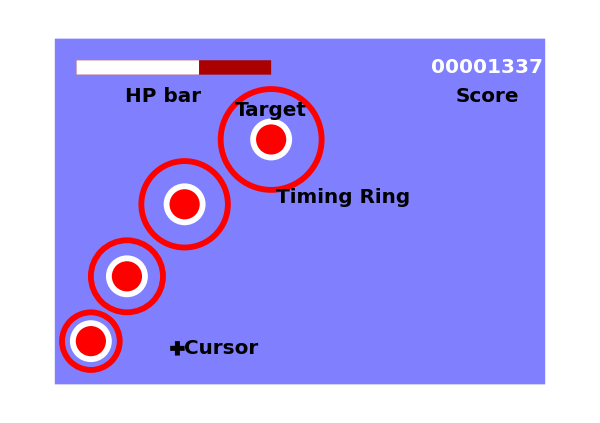

Part::partd: Part specification Null⟦1⟧ is longer than depth of object. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/partd",
ButtonNote->"Part::partd"]

Part::partd: Part specification Null ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
Graphics[{{Lighter[Blue,.5],Rectangle[{0,0},{680,480}]},

{Darker[Red],Rectangle[{30,430},{300,450}]},
{White,Rectangle[{30,430},{200,450}]},
Map[{EdgeForm[{White,Thickness[.007]}],#[[1]],Thickness[.007],Disk[#[[2]],25],Circle[#[[2]],#[[3]]]}&,
{{Red,{50,60},40},
{Red,{100,150},50},
{Red,{180,250},60},
{Red,{300,340},70}
}],

Text[Style["00001337",White,20,Bold],{600,440}],
{Thickness[.006],Line[{{{160,50},{180,50}},{{170,40},{170,60}}}]},
{Black,Text[Style["HP bar",Bold,20],{150,400}]},
{Black,Text[Style["Score",Bold,20],{600,400}]},
{Black,Text[Style["Target",Bold,20],{300,380}]},
{Black,Text[Style["Timing Ring",Bold,20],{400,260}]},
{Black,Text[Style["Cursor",Bold,20],{230,50}]}
}, PlotRange->{{0,680},{0,480}},ImageSize->600]
```

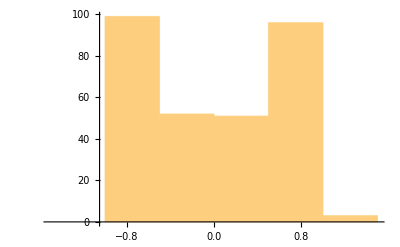

```mathematica
Histogram[%3]
```

```mathematica
3=>2
```

```mathematica
3
```

```mathematica
4:=2
```

SetDelayed::setraw: Cannot assign to raw object 4.

$Failed

```mathematica
2:>
```

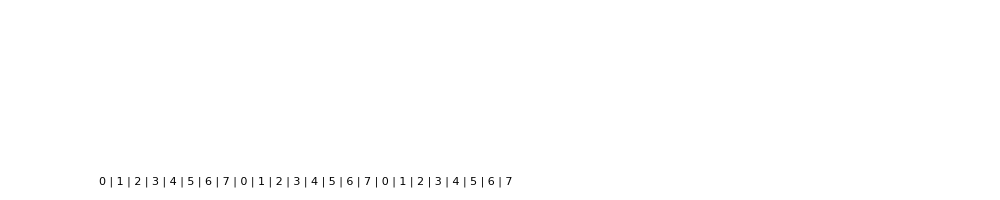

```mathematica
Graphics[Inset[Grid[{Table[Style[Mod[x,8],20,Bold],{x,0,23}]},FrameStyle->Thick,Frame->All,ItemSize->{1.5,1.5},Background->{Table[{Lighter[Red],Lighter[Yellow],Green}[[Quotient[x,8]+1]],{x,0,23}],None}]],ImageSize->1000,PlotRange->{{0,1000},{0,1000/24}}]
```

```mathematica
Graphics[Inset[Grid[{Table[Style[Mod[x,8],20,Bold],{x,0,7}]},FrameStyle->Thick,Frame->All,ItemSize->{1.5,1.5},Background->{{Lighter[Green],Lighter[Green],Lighter[Green],Lighter[Red],Lighter[Red],Lighter[Red],Lighter[Red],Lighter[Red]},None}]],ImageSize->1000,PlotRange->{{0,1000},{0,1000/24}}]
```

-Graphics-

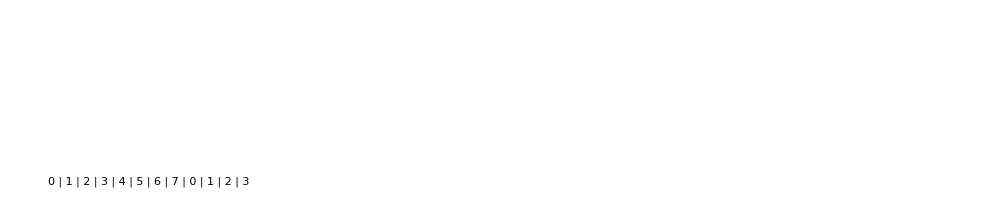

```mathematica
Graphics[Inset[Grid[{Table[Style[Mod[x,8],20,Bold],{x,0,11}]},FrameStyle->Thick,Frame->All,ItemSize->{1.5,1.5},Background->{Table[{Lighter[Red],Lighter[Yellow],Green}[[Quotient[x,8]+1]],{x,0,23}],None}]],ImageSize->1000,PlotRange->{{0,1000},{0,1000/24}}]
```